#### 23.05.2021 (Визуализация случайных блужданий и тензора инерции (Pellisetto))

Грубая программа запуска случайных блужданий

```mathematica
SAW={{0,0}};
n=100;
i=1;
step=0;


While[(i<n)&&(step<2n)&&(i>0),
Neigh =Table[Last[SAW]+turn,{turn,{{0,1},{0,-1},{1,0},{-1,0}}}];
For[j=4,j>0,j--,
If[MemberQ[SAW,Neigh[[j]]],Neigh=Delete[Neigh, j]];];
If[Length[Neigh]>0,,AppendTo[Neigh,"del"]];
new=RandomChoice[Neigh];
SAW=If[StringQ[new],Delete[SAW,Length[SAW]],Append[SAW,new]];
i=Length[SAW];
step=step+1;
];



If[i==0,Print["Не повезло-не повезло"]];
If[i==n,Print["Повезло-повезло"]];
If[0<i<n,Print["Не совсем повезло: ", i]];
```

Повезло-повезло

Получили график случайного блуждания

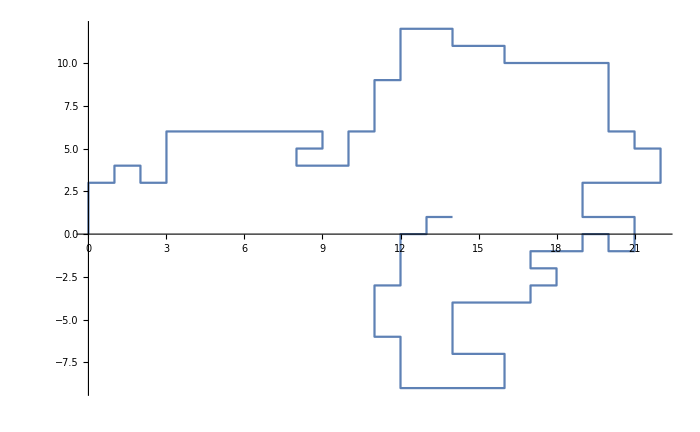

```mathematica
walk=ListPlot[SAW,Joined->True,ImageSize->700,PlotRange->All]
```

Находим параметры полученного блуждания (арифметический центр блуждания, радицс инерции, тензор инерции)

```mathematica
center=Total[SAW]/Length[SAW]
```

{329/25,97/50}

```mathematica
Rg2=N[Total[Map[Norm[#-center]^2&,SAW]]/Length[SAW]]
```

69.4308

```mathematica
n=Length[SAW];
Q=Array[1/(2n^2)*Total[Table[(SAW[[i]][[#1]]-SAW[[j]][[#1]])(SAW[[i]][[#2]]-SAW[[j]][[#2]]),{i,1,n},{j,1,n}],2]&,{2,2}]
```

{{22309/625,-1594/625},{-1594/625,84341/2500}}

```mathematica
Q//MatrixForm
```

(22309/625 | -1594/625
-1594/625 | 84341/2500)

Найдём собственные значения (размеры полуосей) и Жорданов базис (для определения поворота эллипса)

```mathematica
qs=N[Eigenvalues[Q]]
```

{37.4472,31.9836}

```mathematica
S=Map[Normalize,N[Eigenvectors[Q]]]
```

{{-0.824126,0.566407},{0.566407,0.824126}}

```mathematica
N[Inverse[Transpose[S]].Q.Transpose[S]]
```

{{37.4472,3.55271×10^-15},{1.77636×10^-15,31.9836}}

```mathematica
α= ArcCos[S[[1]][[1]]]
```

2.53945

```mathematica
ell2=Graphics[Rotate[Circle[center,√qs],α]];
```

```mathematica
Show[walk,ell2,PlotRange->All]
```

-Graphics-

#### Расчёты показывают, что полученный эллипс не охватывает все точки модели, а лишь занимает “среднее значение”, ближе к наиболее густому участку блуждания. Воспользуемся тривиальным случаем - окружностью.

```mathematica
SAW=Table[{5*Cos[t],5*Sin[t]},{t,0,2Pi,0.1}];
```

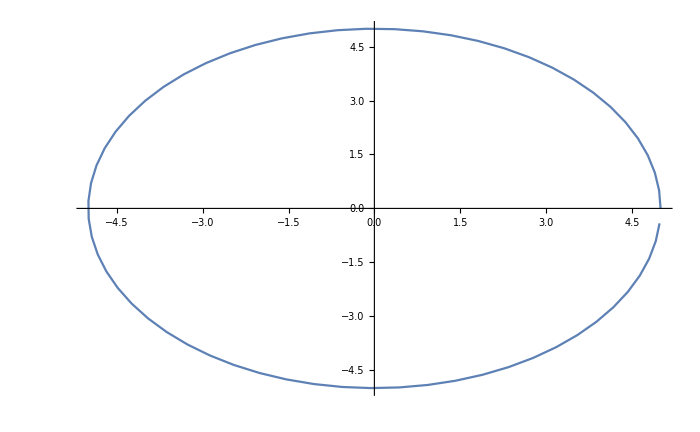

```mathematica
walk=ListPlot[SAW,Joined->True,ImageSize->700,PlotRange->All]
```

Находим параметры полученного блуждания (арифметический центр блуждания, радицс инерции, тензор инерции)

```mathematica
center=Total[SAW]/Length[SAW]
```

{0.0133389,-0.000555118}

```mathematica
Rg2=N[Total[Map[Norm[#-center]^2&,SAW]]/Length[SAW]]
```

24.9998

```mathematica
n=Length[SAW];
Q=Array[1/(2n^2)*Total[Table[(SAW[[i]][[#1]]-SAW[[j]][[#1]])(SAW[[i]][[#2]]-SAW[[j]][[#2]]),{i,1,n},{j,1,n}],2]&,{2,2}]
```

{{12.5331,-0.00276916},{-0.00276916,12.4667}}

```mathematica
Q//MatrixForm
```

(12.5331 | -0.00276916
-0.00276916 | 12.4667)

Найдём собственные значения (размеры полуосей) и Жорданов базис (для определения поворота эллипса)

```mathematica
qs=N[Eigenvalues[Q]]
```

{12.5332,12.4666}

```mathematica
S=Map[Normalize,N[Eigenvectors[Q]]]
```

{{-0.999135,0.0415807},{-0.0415807,-0.999135}}

```mathematica
N[Inverse[Transpose[S]].Q.Transpose[S]]
```

{{12.5332,0.},{0.,12.4666}}

```mathematica
α= ArcCos[S[[1]][[1]]]
```

3.1

```mathematica
ell2=Graphics[Rotate[Circle[center,√qs],α]];
```

```mathematica
Show[walk,ell2,PlotRange->All]
```

-Graphics-

#### ?????????